```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 237 Kb

{Utilities`CleanSlate`,Parallel`Debug`Perfmon`,Parallel`Debug`,CompiledFunctionTools`,IPOPTLink`,VariationalMethods`,System`,Global`}

```mathematica
Clear[rm]
rm = { R Sin[θ[t]] + R Sin[ϕ[t]] , R Cos[θ[t]] + R Cos[ϕ[t]] }
```

{R Sin[θ[t]]+R Sin[ϕ[t]],R Cos[θ[t]]+R Cos[ϕ[t]]}

```mathematica
D[rm, t]
```

{R Cos[θ[t]] θ'[t]+R Cos[ϕ[t]] ϕ'[t],-R Sin[θ[t]] θ'[t]-R Sin[ϕ[t]] ϕ'[t]}

```mathematica
D[rm, t] . D[rm, t]
```

(R Cos[θ[t]] θ'[t]+R Cos[ϕ[t]] ϕ'[t])^2+(-R Sin[θ[t]] θ'[t]-R Sin[ϕ[t]] ϕ'[t])^2

```mathematica
D[rm, t] . D[rm, t]  // Expand
```

R^2 Cos[θ[t]]^2 θ'[t]^2+R^2 Sin[θ[t]]^2 θ'[t]^2+2 R^2 Cos[θ[t]] Cos[ϕ[t]] θ'[t] ϕ'[t]+2 R^2 Sin[θ[t]] Sin[ϕ[t]] θ'[t] ϕ'[t]+R^2 Cos[ϕ[t]]^2 ϕ'[t]^2+R^2 Sin[ϕ[t]]^2 ϕ'[t]^2

```mathematica
D[rm, t] . D[rm, t]  // Expand  // Simplify
```

R^2 (θ'[t]^2+2 Cos[θ[t]-ϕ[t]] θ'[t] ϕ'[t]+ϕ'[t]^2)

```mathematica
Clear[rM]
rM = { R Sin[θ[t]] , R Cos[θ[t]] }
```

{R Sin[θ[t]],R Cos[θ[t]]}

```mathematica
D[rM, t]
```

{R Cos[θ[t]] θ'[t],-R Sin[θ[t]] θ'[t]}

```mathematica
D[rM, t] . D[rM, t]
```

R^2 Cos[θ[t]]^2 θ'[t]^2+R^2 Sin[θ[t]]^2 θ'[t]^2

```mathematica
D[rM, t] . D[rM, t]  // Simplify
```

R^2 θ'[t]^2

```mathematica
Clear[T]
T = 1/2 m ( D[rm, t] . D[rm, t]  // Expand  // Simplify  ) + 1/2 M ( D[rM, t] . D[rM, t]  // Simplify  )+ 1/2( M R^2 ) θ'[t]^2 ;
T // Simplify // pdConv
```

1/2 R^2 ((m+2 M) ((∂θ(t))/(∂t))^2+2 m (∂θ(t))/(∂t) (∂ϕ(t))/(∂t) cos(θ(t)-ϕ(t))+m ((∂ϕ(t))/(∂t))^2)

```mathematica
(* Their sign convention for V isn't consistent *)
```

```mathematica
rm
rm[[2]]
```

{R Sin[θ[t]]+R Sin[ϕ[t]],R Cos[θ[t]]+R Cos[ϕ[t]]}

R Cos[θ[t]]+R Cos[ϕ[t]]

```mathematica
Clear[Vm]
Vm =-  m g rm[[2]]
```

-g m (R Cos[θ[t]]+R Cos[ϕ[t]])

```mathematica
rM
rM[[2]]
```

{R Sin[θ[t]],R Cos[θ[t]]}

R Cos[θ[t]]

```mathematica
Clear[VM]
VM = - M g rM[[2]]
```

-g M R Cos[θ[t]]

```mathematica
Clear[V]
V =Vm + VM
```

-g M R Cos[θ[t]]-g m (R Cos[θ[t]]+R Cos[ϕ[t]])

```mathematica
Clear[ℒ]
ℒ = T - V  ; 
ℒ // pdConv
```

g m (R cos(θ(t))+R cos(ϕ(t)))+g M R cos(θ(t))+1/2 m R^2 (2 (∂θ(t))/(∂t) (∂ϕ(t))/(∂t) cos(θ(t)-ϕ(t))+((∂θ(t))/(∂t))^2+((∂ϕ(t))/(∂t))^2)+M R^2 ((∂θ(t))/(∂t))^2

```mathematica
Clear[q]
q = { θ[t] , ϕ[t] }
```

{θ[t],ϕ[t]}

```mathematica
D[ D[ ℒ , D[q[[1]], t] ], t ]  - D[ ℒ , q[[1]] ] // Expand // Simplify 
D[ D[ ℒ , D[q[[2]], t] ], t ]  - D[ ℒ , q[[2]] ] // Expand // Simplify
```

R (g m Sin[θ[t]]+g M Sin[θ[t]]+m R Sin[θ[t]-ϕ[t]] ϕ'[t]^2+(m+2 M) R θ''[t]+m R Cos[θ[t]-ϕ[t]] ϕ''[t])

m R (g Sin[ϕ[t]]-R Sin[θ[t]-ϕ[t]] θ'[t]^2+R Cos[θ[t]-ϕ[t]] θ''[t]+R ϕ''[t])

```mathematica
Table[
D[ D[ ℒ , D[q[[i]], t] ], t ]  - D[ ℒ , q[[i]] ] // Expand // Simplify  , 
{ i, 1, 2 } ]  // TableForm
```

R (g m Sin[θ[t]]+g M Sin[θ[t]]+m R Sin[θ[t]-ϕ[t]] ϕ'[t]^2+(m+2 M) R θ''[t]+m R Cos[θ[t]-ϕ[t]] ϕ''[t])
m R (g Sin[ϕ[t]]-R Sin[θ[t]-ϕ[t]] θ'[t]^2+R Cos[θ[t]-ϕ[t]] θ''[t]+R ϕ''[t])

```mathematica
Clear[eqs]
eqs = 
EulerEquations[ ℒ , q , t ] ;
eqs // TableForm
```

-R (g m Sin[θ[t]]+g M Sin[θ[t]]+m R Sin[θ[t]-ϕ[t]] ϕ'[t]^2+(m+2 M) R θ''[t]+m R Cos[θ[t]-ϕ[t]] ϕ''[t])==0
-m R (g Sin[ϕ[t]]-R Sin[θ[t]-ϕ[t]] θ'[t]^2+R Cos[θ[t]-ϕ[t]] θ''[t]+R ϕ''[t])==0

```mathematica
Clear[parameters]
parameters = { 
m -> 2 , 
M -> 20 , 
g -> 9.8 , 
R -> 1.5  
} ;
parameters // TableForm
```

m→2
M→20
g→9.8
R→1.5

```mathematica
eqs /. parameters // Expand // TableForm
```

-323.4 Sin[θ[t]]-4.5 Sin[θ[t]-ϕ[t]] ϕ'[t]^2-94.5 θ''[t]-4.5 Cos[θ[t]-ϕ[t]] ϕ''[t]==0
-29.4 Sin[ϕ[t]]+4.5 Sin[θ[t]-ϕ[t]] θ'[t]^2-4.5 Cos[θ[t]-ϕ[t]] θ''[t]-4.5 ϕ''[t]==0

```mathematica
Clear[ics]
ics = { 
θ[0] == 0.1 , 
θ'[0] == 0 , 
ϕ[0] == 0 , 
ϕ'[0] == 0 
} ; 
ics // TableForm
```

θ[0]==0.1
θ'[0]==0
ϕ[0]==0
ϕ'[0]==0

```mathematica
Clear[solution]
solution[t_] = 
First[ NDSolve[ Union[ eqs /. parameters , ics ] , q , { t, 0, 300 } ] ]
```

{θ[t]→InterpolatingFunction[…][t],ϕ[t]→InterpolatingFunction[…][t]}

```mathematica
Plot[ Evaluate[ q /. solution[t]]  , { t, 0, 10 } , PlotLabels-> q  ]
```

-Graphics-

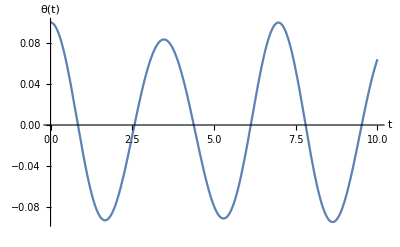

```mathematica
Plot[ q[[1]] /. solution[t] , { t, 0, 10 } , AxesLabel-> { t, q[[1]] } ]
```

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[1,2]] , solution'[t][[1,2]] } , { t , 0, tmax } , AxesLabel-> { q[[1]] , D[q[[1]], t] } ]  ,
{ tmax , 0.01 ,50   } ]
```

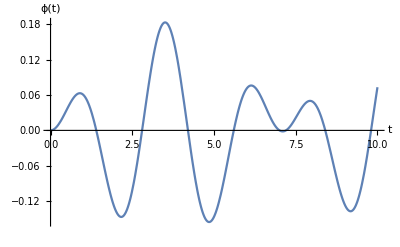

```mathematica
Plot[ q[[2]] /. solution[t] , { t, 0, 10 } , AxesLabel-> { t, q[[2]] }]
```

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[2,2]] , solution'[t][[2,2]] } , { t , 0, tmax } , AxesLabel-> { q[[2]] , D[q[[2]], t] } ]  ,
{ tmax , 0.01 ,50   } ]
```

```mathematica
eqs
```

{-R (g m Sin[θ[t]]+g M Sin[θ[t]]+m R Sin[θ[t]-ϕ[t]] ϕ'[t]^2+(m+2 M) R θ''[t]+m R Cos[θ[t]-ϕ[t]] ϕ''[t])==0,-m R (g Sin[ϕ[t]]-R Sin[θ[t]-ϕ[t]] θ'[t]^2+R Cos[θ[t]-ϕ[t]] θ''[t]+R ϕ''[t])==0}

```mathematica
Manipulate[
DynamicModule[{solution1} ,
solution1 = NDSolve[ { A y''[t] + ω^2 y[t] == 0 , y[0] == 2 , y'[0] == 2 } , y[t] , { t, 0, 10 } ] ;
Plot[y[t] /.  solution1 , { t , 0, 10 } , PlotRange-> { -16 , 16 }  ] ],
{ ω , 0.1 , 0.2 }, { A , 0.1  , 0.2 }  ]
```

```mathematica
Union[ eqs , ics ]
```

{θ[0]==0.1,ϕ[0]==0,θ'[0]==0,ϕ'[0]==0,-m R (g Sin[ϕ[t]]-R Sin[θ[t]-ϕ[t]] θ'[t]^2+R Cos[θ[t]-ϕ[t]] θ''[t]+R ϕ''[t])==0,-R (g m Sin[θ[t]]+g M Sin[θ[t]]+m R Sin[θ[t]-ϕ[t]] ϕ'[t]^2+(m+2 M) R θ''[t]+m R Cos[θ[t]-ϕ[t]] ϕ''[t])==0}

```mathematica
?NDSolveValue
```

```mathematica
(* Interactively Solve PDE's *)
```

```mathematica
eqn = -Inactive[Div][(1/Sqrt[1 + ∇_{x,y} u[x,y].∇_{x,y} u[x,y]]) Inactive[Grad][
       u[x, y], {x, y}], {x, y}] == 0
```

-((u[x,y]{x,y}Inactive)/(√(1+(u^(0,1)[x,y])^2+(u^(1,0)[x,y])^2)){x,y}Inactive)==0

```mathematica
bc=DirichletCondition[u[x,y]==Sin[2 π*(x+y)],True]
```

DirichletCondition[u[x,y]==Sin[2 π (x+y)],True]

```mathematica
NDSolveValue[{eqn,bc},u,{x,y}∈Disk[]]
```

InterpolatingFunction[…]

```mathematica
NDSolveValue[{eqn,bc},u,{x,y}∈Disk[]];
Plot3D[%[x,y],{x,y}∈Disk[],Sequence[ColorFunction->ColorData["SouthwestColors"],"ImageSize"->Medium]]
```

-Graphics3D-

```mathematica
Manipulate[DynamicModule[{ifun},mesh=NDSolve`FEM`ToElementMesh[RegionDifference[Disk[],Rectangle[p-1/4,p+1/4]],{{-1.1,1.1},{-1.1,1.1}}];
ifun=NDSolveValue[{eqn,bc},u,{x,y}∈mesh];
Plot3D[ifun[x,y],{x,y}∈ifun["ElementMesh"],Sequence[ColorFunction->ColorData["SouthwestColors"],PlotRange->{-1,1},Boxed->False,Axes->False]]],{p,{-1/2,-1/2},{1/2,1/2}},ContinuousAction->False]
```